### VISMAYA WALAWALKAR ME454, Spring 2017 FINAL PROJECT

# Optimal Control of Inverted Pendulum on a Hovering Plate in 2D: Simplified

Note : Run time = 20 mins

```mathematica
g=9.81; 
m0=1; 
m1=0.1;
L=1; 

(* Define trajectories with dimensions *)
x= Table[xt[i][t],{i,1,6}];
P[t_]:= Table[Pt[i,j][t],{i,1,6},{j,1,6}];
r[t_]:= {{r11[t]},{r12[t]},{r13[t]},{r14[t]} ,{r15[t]},{r16[t]}};
z[t_]:= {{z11[t]},{z12[t]},{z13[t]},{z14[t]},{z15[t]},{z16[t]}};

(* Initial Conditions *)
P1= DiagonalMatrix[{0,0,0,0,0,0}];(*{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}};*)
r1={{0,0,0,0,0,0}}ᵀ;
z1={{0,0,0,0,0,0}}ᵀ;

(* Define system Dynamics *)
(*fx = {
x[[2]],

(L m1 Sin[x[[3]]] (x[[4]])^2  + u - g m1 Cos[x[[3]]] Sin[x[[3]]])/(m0 + m1 - m1 Cos[x[[3]]]^2), 

x[[4]],

-(L m1 Cos[x[[3]]] Sin[x[[3]]] (x[[4]])^2 + u* Cos[x[[3]]] - g(m0+m1) Sin[x[[3]]])/(L(m0+m1-m1 (Cos[x[[3]]])^2))};*)

fx = {
x[[2]],

u1,

x[[4]],

( (g+u1)*Sin[x[[3]]]  - u2*Cos[x[[5]]] )/L,

x[[6]],

u2
};

(* Define Cost function *)
Q=DiagonalMatrix[{200,0,200,0,200,0}];
R={{0.3, 0}, {0,0.3}};
xd={{50,0,π,0,0,0}}ᵀ;
xs={{x[[1]],0,x[[3]],0, x[[5]], 0}}ᵀ;
 
costL=((xs-xd)ᵀ.Q.(xs-xd) + {{u1, u2}}.R.{{u1, u2}}ᵀ )[[1,1]];

(* Solve for x *)
xdot=D[x,t];
xeqs=Thread[xdot== fx];
(* Assume the passenger is almost upright *)
xinit= Thread[(x/.t-> 0)== {0,0,0.1, 0,0,0}];
xsol[ut1_, ut2_]:=NDSolve[{xeqs/.u1->ut1 /. u2->ut2, xinit},x,{t,0,5}][[1]];
```

```mathematica
(* Solve for Matrices *)
A=D[fx,{x}];
B={Flatten[D[fx,u1]],Flatten[ D[fx,u2]]}ᵀ;
a={D[costL,{x}]}ᵀ;
b={{D[costL,u1], D[costL,u2]}}ᵀ;

(* Solve for P *)
Psol[ut1_, ut2_] := P[t]/. NDSolve[{-P'[t]== (Aᵀ.P[t]+ P[t].A -P[t].B.Inverse[R].Bᵀ.P[t] + Q)/.xsol[ut1,ut2]/.u1->ut1 /. u2->ut2,Thread[P[5]== P1]},Flatten[P[t]], {t,0,5}][[1]];

(* Solve for r *)
rsol[ut1_, ut2_,pt_]:= r[t]/.NDSolve[{-r'[t]== Flatten[((A-B.Inverse[R].Bᵀ.pt)ᵀ.r[t]+ a-pt.B.Inverse[R].b)/.xsol[ut1,ut2]/.u1->ut1 /. u2->ut2],Thread[r[5]==r1]},Flatten[r[t]],{t,0,5}][[1]];

(* Solve for z *)
zsol[ut1_, ut2_,pt_,rt_]:= z[t]/.NDSolve[{(z'[t]== A.z[t] + B.(-Inverse[R].Bᵀ.pt.z[t] -Inverse[R].Bᵀ.rt-Inverse[R].b))/.xsol[ut1,ut2]/.u1->ut1 /. u2->ut2,z[0]== z1 },Flatten[z[t]],{t,0,5}][[1]];

(* Solve for v *)
vsol[ut1_, ut2_,pt_,rt_,zt_]:=(-Inverse[R].Bᵀ.pt.zt -Inverse[R].Bᵀ.rt-Inverse[R].b)/.xsol[ut1,ut2]/.u1->ut1 /. u2->ut2;
```

```mathematica
(* Test Values *)
u10= 0;
u20 = 0;

solx0=xsol[u10,u20];
Plot[x/.solx0,{t,0,5}, PlotLabel->"X[t]",PlotRange->All];
P0=Psol[u10,u20];
Plot[P0, {t,0,5},PlotLabel->"P[t]",PlotRange->All];
r0=rsol[u10, u20,P0];
Plot[r0,{t,0,5},PlotLabel->"r[t]", PlotRange->All];
z0=zsol[u10, u20,P0,r0];
Plot[z0,{t,0,5},PlotLabel->"z[t]",PlotRange->All];
v0=vsol[u10, u20,P0,r0,z0];
Plot[v0,{t,0,5},PlotLabel->"v[t]",PlotRange->All];
```

```mathematica
(* J and DJ *)
J[ut1_, ut2_]:= NIntegrate[costL/.(x[[1]])-> (x[[1]]/.xsol[ut1, ut2])/.(x[[3]])-> (x[[3]]/.xsol[ut1, ut2]) /. (x[[5]])-> (x[[5]]/.xsol[ut1, ut2])/.u1-> ut1 /.u2-> ut2,{t,0,5}];

DJ[ut1_, ut2_,zt_,vt_]:=  NIntegrate[(aᵀ.zt+ bᵀ.vt)/.xsol[ut1, ut2]/.u1-> ut1 /.u2-> ut2,{t,0,5}][[1,1]];

(* Test Values *)
J[2,1]
DJ[0,1,z0,v0]
```

1.82295×10^6

-9.43918×10^6

```mathematica
(* Line Search *)
Armijo[u10_, u20_,vi_,zi_]:= Module[{α = 0.4,β = 0.7, n = 0,γ = β^n, utest1, utest2},
 γ=β^n;
{utest1, utest2}= Flatten[{{u10, u20}}ᵀ+γ*vi];
While[J[utest1, utest2]> J[u10, u20]+α*γ*DJ[u10, u20,zi,vi],     
{utest1, utest2}= Flatten[{{u10, u20}}ᵀ+γ*vi];
γ=β^ n;
n++;
];
Return[γ]
];

(* Test Values *)
Armijo[0,0.5, v0, z0]
```

0.0823543

```mathematica
(* iLQR loop *)
ii=0; 
u10=0;
u20=0;
ζi=1000;
ϵ=0.05;

Print[J[u10, u20]];

While[Abs[ζi]>ϵ,

pi=Psol[u10,u20];
ri=rsol[u10,u20,pi];
zi=zsol[u10,u20,pi,ri];
vi=vsol[u10,u20, pi,ri,zi];

γi=Armijo[u10, u20,vi,zi];

{u1i, u2i}= Flatten[{{u10, u20}}ᵀ+γi*vi];
(*ui=u0+γi*vi; *)
x0=xsol[u10, u20];

u1list=Table[u1i/.t-> i, {i,0,5,0.01}];
u2list=Table[u2i/.t-> i, {i,0,5,0.01}];
u10=ListInterpolation[u1list, {0,5}][t];
u20=ListInterpolation[u2list, {0,5}][t];

ii++;

ζi =Norm[NIntegrate[zi,{t,0,5}, Method->"MultiPeriodic"]]+Norm[NIntegrate[(vi/.u1-> u10 /.u2-> u20),{t,0,5}, Method->"MultiPeriodic"]];
Print[Abs[ζi]];
];
Print[{ii, J[u10, u20]}];
```

2.5057×10^6

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in t in the region {{0.,1.}}. NIntegrate obtained 0.0892173 and 2.41218×10^-6 for the integral and error estimates.

487.135

318.304

157.97

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in t in the region {{0.,1.}}. NIntegrate obtained 1.0299 and 1.71295×10^-6 for the integral and error estimates.

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in t in the region {{0.,1.}}. NIntegrate obtained 0.366531 and 8.53382×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvi will be suppressed during this calculation.

69.1519

39.4452

70.7996

52.4556

69.7183

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.0586065}. NIntegrate obtained -19185.7 and 0.0810869 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

17.0829

21.7028

19.7915

17.9629

16.4304

14.6281

11.9924

8.24938

6.43742

3.37653

0.567905

0.0525074

0.0432204

$Aborted

{21,140969.}

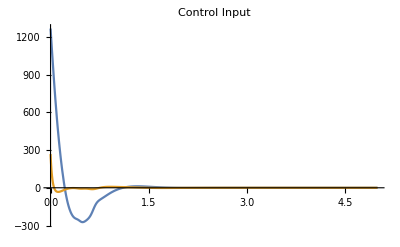

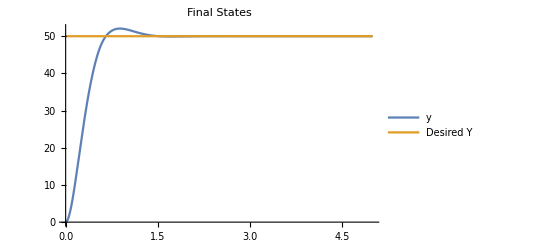

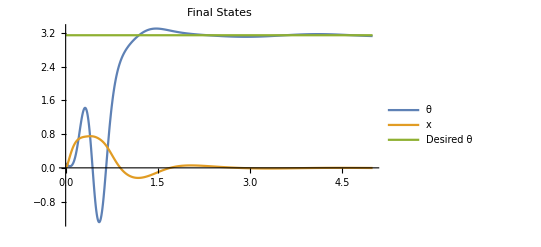

```mathematica
Plot[{u10, u20}, {t,0,5},PlotRange->Full,PlotLabel-> "Control Input"]
Plot[{x[[1]]/.x0, xd[[1]]},{t,0,5},PlotRange->Full,PlotLabel-> "Final States", PlotLegends->{"y", "Desired Y"}]
Plot[{ x[[3]]/.x0, x[[5]]/.x0, xd[[3]]},{t,0,5},PlotRange->Full,PlotLabel-> "Final States", PlotLegends->{"θ", "x", "Desired θ"}]
```